### Define the Parameters

```mathematica
ClearAll[c,λ,ω, k, T, rfAmp, rfFre, Vpi, V0, Pmax, Pmin,ϵ]
```

ClearAll::ssym: k T rfAmp is not a symbol or a string.

```mathematica
c = 299792458;(*speed of light m/s*)
λ = 637.23*10^-9;(*laser wavelength m*)
ω = 2π c/λ; (*angular frequency rad/s*)
k  = 2π/λ; (*wave number*)
T = 2π/ω;(*period*)
ϵ = 8.854*10^-12; (*vacuum permittivity*)
rfAmp = 3;(*RF amplitude in V*)
rfAmp = 2;(*RF amplitude in V*)
rfFre = 500*10^6;(*RF frequency in Hz*)
rfFre2 = 200*10^6;(*RF frequency2 in Hz*)
Vpi = 3; (*half-wave voltage*)
V0 = 0; (*operation voltage of the EOM (offset)*)
Pmax=1; (*maximum laser power after EOM, mW*)
Pmin= 0 ;(*Pmax/500minimum laser power after EOM, mW*)
```

### Define equations

```mathematica
ClearAll[t,Laser, Modulation]
```

```mathematica
Modulation = rfAmp Cos[2π rfFre t]+rfAmp2 Cos[2π rfFre2 t];
Laser[p_] = Sqrt[2*p/(c*ϵ)]* Exp[I(k x - ω t)];
```

### Plot the equations

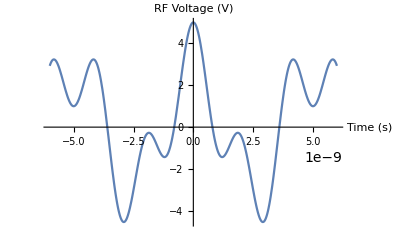

```mathematica
Plot[Modulation, {t,-3/rfFre,3/rfFre}, AxesLabel->{ "Time (s)","RF Voltage (V)"}]
```

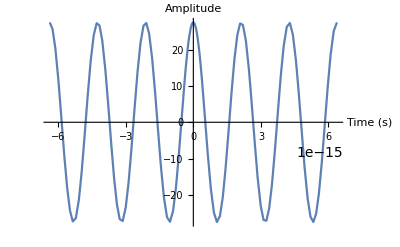

```mathematica
Plot[Re[Laser[1]/.{x->0}], {t,-3*2π/ω,3*2π/ω}, AxesLabel->{ "Time (s)","Amplitude"},PlotRange->All]
```

### Apply Modulation to Laser

```mathematica
EOM = Laser[1]*Modulation/.x->0
```

27.4495 ⅇ^(ⅈ (0.-2.956×10^15 t)) (3 Cos[400000000 π t]+2 Cos[1000000000 π t])

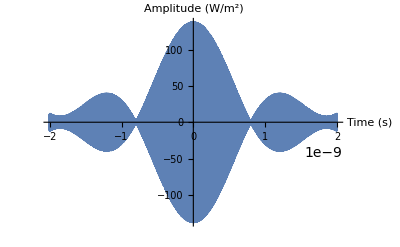

```mathematica
Plot[Re[EOM],{t,-1/rfFre,1/rfFre} ,AxesLabel->{ "Time (s)","Amplitude (W/m^2)"},PlotRange->All,PlotPoints->10000]
```

## Go to the Frequency Space

```mathematica
frequencyEOM = FullSimplify[FourierTransform[EOM,t,w]]
```

68.8058 DiracDelta[2.956×10^15-w]+103.209 DiracDelta[2.956×10^15-w]+103.209 DiracDelta[2.956×10^15-w]+68.8058 DiracDelta[2.956×10^15-w]

```mathematica
frequencyLaser= FullSimplify[FourierTransform[Laser[1]/.x->0,t,w]]
```

68.8058 DiracDelta[2.956×10^15-w]

```mathematica
fwhm=100*10^6;(*FWHM for a Gaussian distribution*)
sigma=fwhm/(2 Sqrt[2 Log[2]]);
amplitude=1;
gaussian=amplitude Exp[-(w^2/(2 sigma^2))];
laserSpectrum = Convolve[frequencyLaser,gaussian,w,o]
EOMSpectrum=Convolve[frequencyEOM,gaussian,w,o]
```

68.8058 2^(-4.×10^-16 (-2.956×10^15+o)^2)

68.8058 2^(-4.×10^-16 (-2.956×10^15+o)^2)+103.209 2^(-4.×10^-16 (-2.956×10^15+o)^2)+103.209 2^(-4.×10^-16 (-2.956×10^15+o)^2)+68.8058 2^(-4.×10^-16 (-2.956×10^15+o)^2)

```mathematica
(*Plot[Evaluate[frequencyEOM/. DiracDelta[a_]:> UnitStep[1/100000-10a^2]],{w,ω-10^9*(π),ω+10^9*(π)},Exclusions->None,PlotPoints->20000,PlotRange->{{ω-10^9*(2π),ω+10^9*(2π)},{0,100000}}]*)
```

```mathematica
Plot[laserSpectrum,{o,ω-10^9*(π),ω+10^9*(π)},PlotRange->All]
```

General::munfl: 1/2^3947.52 is too small to represent as a normalized machine number; precision may be lost.

-Graphics-

```mathematica
Plot[EOMSpectrum,{o,ω-0.6*10^9*(2π),ω+0.6*10^9*(2π)},PlotRange->All]
```

General::munfl: 1/2^19106.7 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1/2^10105.9 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1/2^2526.31 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

-Graphics-